## Some notes for Section 8.3 of Bernevig’s book

Producing fig.8.2:

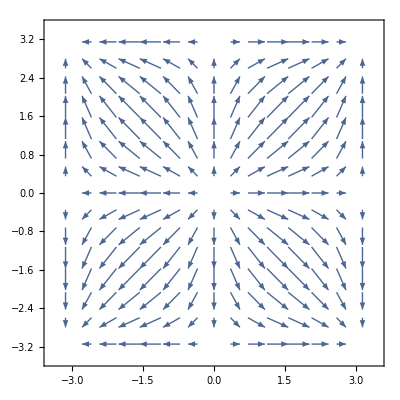

```mathematica
VectorPlot[{Sin[kx],Sin[ky]},{kx,-π,π},{ky,-π,π}]
```

The vector plot in fig.8.4:

```mathematica
VectorPlot3D[{Sin[kx],Sin[ky],(2+-1-Cos[kx]-Cos[ky])},{kx,-π,π},{ky,-π,π},{kz,-2,2}]
```

-Graphics3D-

```mathematica
SliceVectorPlot3D[{Sin[kx],Sin[ky],(2+-1-Cos[kx]-Cos[ky])}, {z==0},{kx,-2,2},{ky,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
Manipulate[SliceVectorPlot3D[{Sin[kx],Sin[ky],(2+M-Cos[kx]-Cos[ky])}, {z==0},{kx,-2,2},{ky,-2,2},{z,-2,2}],
{M,-5,1}]
```